Graph states (also known as cluster states) are a specific class of multi-qubit entangled states that are defined based on graphs. Graph states are foundational to the one-way quantum computing model (measurement-based quantum computing), where quantum computation is achieved through a sequence of adaptive measurements on an initial graph state.

Generate a random graph with 4 vertexes and 5 edges. Each vertex of the graph corresponds to a qubit, and the edges represent entanglement between the qubits:

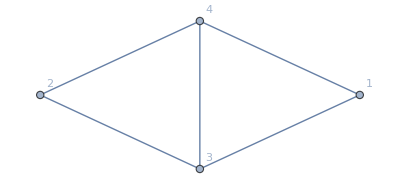

```mathematica
g=RandomGraph[{4,5},VertexLabels->Automatic]
```

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

Create a circuit that generates the corresponding quantum graph state:

```mathematica
qc=QuantumCircuitOperator[{"Graph",g}]
```

-Graphics-

Show the circuit diagram:

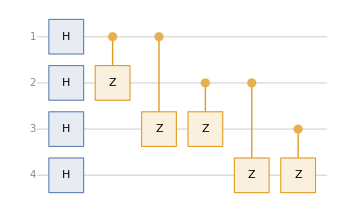

```mathematica
qc["Diagram"]
```

Show that the circuit acting on a register state creates the expected quantum cluster/graph state:

```mathematica
ψf=qc[]
```

QuantumState[…]

```mathematica
ψf==QuantumState[{"Graph",g}]
```

True

Show that qubits connected via an edge are entangled:

```mathematica
QuantumEntangledQ[ψf,{#1,#}]&@@@EdgeList[g]
```

{True,True,True,True,True}

Given a vertex of the graph, find the list of vertices adjacent to it:

```mathematica
verAdj=Transpose[Through[{VertexList,AdjacencyList}[g]]]
```

{{1,{2,3}},{2,{1,3,4}},{3,{1,2,4}},{4,{2,3}}}

Now let's find stabilizers, which are simply a set of operators that represent the symmetries of a quantum state. Given the above list of vertices and their adjacencies find the stabilizers, which can be obtained by Pauli-X on vertex and Pauli-Z on adjacencies:

```mathematica
stabilizers=QuantumOperator[{"X"->#1,"Z"->#2}]&@@@verAdj
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

Apply the above list of stabilizers and show that the result is still the same as the original state (that is why it is called stabilizer):

```mathematica
Thread[Through[stabilizers[ψf]]==ψf]
```

{True,True,True,True}